```mathematica
(*Uniform model*)
pΘ[Θ_]:=1/Sqrt[2 Pi σθ^2] Exp[-Θ^2/(2 σθ^2)];
pΦ[Φ_]:=1/Pi
pρ[ρ_]:=1/(ρ Sqrt[2 Pi σρ^2])Exp[-Log[ρ]^2/(2 σρ^2)](*Exp[(-(ρ-1)^2)/(2 σρ^2)];*)
```

```mathematica
mean[f_]:=Integrate[f[Θ, Φ, ρ]pΘ[Θ] pΦ[ Φ]pρ[ ρ], {Θ, -Infinity, Infinity}, {Φ, -Pi/2, Pi/2}, {ρ, 0, Infinity}, Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
cov[f1_, f2_]:=Integrate[(f1[Θ, Φ, ρ]-mean[f1])(f2[Θ, Φ, ρ]-mean[f2]) pΘ[Θ]pΦ[Φ]pρ[ ρ], {Θ, -Infinity, Infinity}, {Φ, -Pi/2, Pi/2}, {ρ, 0, Infinity}, Assumptions->{σθ>0, σρ>0,θ>0, ϕ>0}]
```

```mathematica
nv[Θ_, Φ_, ρ_]:={ρ Sin[Θ]Cos[Φ],ρ Sin[Θ]Sin[Φ], ρ Cos[Θ]};
rot=Transpose[{{Cos[-θ], 0, Sin[-θ]}, {0, 1, 0},{-Sin[-θ],0,  Cos[-θ]}}.{{Cos[-ϕ], -Sin[-ϕ], 0}, {Sin[-ϕ], Cos[-ϕ], 0}, {0, 0, 1}}];
fx[Θ_, Φ_, ρ_]:=(rot.nv[Θ, Φ, ρ])[[1]];
fy[Θ_, Φ_, ρ_]:=(rot.nv[Θ, Φ, ρ])[[2]];
fz[Θ_, Φ_, ρ_]:=(rot.nv[Θ, Φ, ρ])[[3]];
```

```mathematica
cxx=Simplify[cov[fx, fx], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
cyy=Simplify[cov[fy, fy], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
czz=Simplify[cov[fz, fz], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
cxy=Simplify[cov[fx, fy], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
cxz=Simplify[cov[fx, fz], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
cyz=Simplify[cov[fy, fz], Assumptions->{σθ>0,σρ>0, θ>0, ϕ>0}]
```

1/8 ⅇ^(-2 σθ^2+σρ^2) (-3 ⅇ^(σρ^2) Cos[θ]^2 Cos[ϕ]^2+3 ⅇ^(2 σθ^2+σρ^2) Cos[θ]^2 Cos[ϕ]^2-16 ⅇ^(σθ^2) Cos[ϕ]^2 Sin[θ]^2+6 ⅇ^(σρ^2) Cos[ϕ]^2 Sin[θ]^2+6 ⅇ^(2 σθ^2+σρ^2) Cos[ϕ]^2 Sin[θ]^2+8 ⅇ^(σθ^2) Cos[ϕ]^2 Erf[σρ/(√2)] Sin[θ]^2+8 ⅇ^(σθ^2) Cos[ϕ]^2 GammaRegularized[1/2,σρ^2/2] Sin[θ]^2-3 ⅇ^(σρ^2) Sin[ϕ]^2+3 ⅇ^(2 σθ^2+σρ^2) Sin[ϕ]^2-ⅇ^(σρ^2) Erf[√2 σρ] ((-1+ⅇ^(2 σθ^2)) Cos[θ]^2 Cos[ϕ]^2+2 (1+ⅇ^(2 σθ^2)) Cos[ϕ]^2 Sin[θ]^2+(-1+ⅇ^(2 σθ^2)) Sin[ϕ]^2)-ⅇ^(σρ^2) GammaRegularized[1/2,2 σρ^2] ((-1+ⅇ^(2 σθ^2)) Cos[θ]^2 Cos[ϕ]^2+2 (1+ⅇ^(2 σθ^2)) Cos[ϕ]^2 Sin[θ]^2+(-1+ⅇ^(2 σθ^2)) Sin[ϕ]^2))

1/8 ⅇ^(-2 σθ^2+σρ^2) (-3 ⅇ^(σρ^2) Cos[ϕ]^2+3 ⅇ^(2 σθ^2+σρ^2) Cos[ϕ]^2-3 ⅇ^(σρ^2) Cos[θ]^2 Sin[ϕ]^2+3 ⅇ^(2 σθ^2+σρ^2) Cos[θ]^2 Sin[ϕ]^2-16 ⅇ^(σθ^2) Sin[θ]^2 Sin[ϕ]^2+6 ⅇ^(σρ^2) Sin[θ]^2 Sin[ϕ]^2+6 ⅇ^(2 σθ^2+σρ^2) Sin[θ]^2 Sin[ϕ]^2+8 ⅇ^(σθ^2) Erf[σρ/(√2)] Sin[θ]^2 Sin[ϕ]^2+8 ⅇ^(σθ^2) GammaRegularized[1/2,σρ^2/2] Sin[θ]^2 Sin[ϕ]^2-ⅇ^(σρ^2) Erf[√2 σρ] ((-1+ⅇ^(2 σθ^2)) Cos[ϕ]^2-1/2 (-1-3 ⅇ^(2 σθ^2)+(3+ⅇ^(2 σθ^2)) Cos[2 θ]) Sin[ϕ]^2)-ⅇ^(σρ^2) GammaRegularized[1/2,2 σρ^2] ((-1+ⅇ^(2 σθ^2)) Cos[ϕ]^2-1/2 (-1-3 ⅇ^(2 σθ^2)+(3+ⅇ^(2 σθ^2)) Cos[2 θ]) Sin[ϕ]^2))

1/8 ⅇ^(-2 σθ^2+σρ^2) (-4 ⅇ^(σθ^2)+ⅇ^(σρ^2) (3+ⅇ^(2 σθ^2))) Sin[θ]^2 Sin[2 ϕ]

1/8 ⅇ^(-2 σθ^2+σρ^2) (-4 ⅇ^(σθ^2)+ⅇ^(σρ^2) (3+ⅇ^(2 σθ^2))) Cos[ϕ] Sin[2 θ]

1/8 ⅇ^(-2 σθ^2+σρ^2) (-4 ⅇ^(σθ^2)+ⅇ^(σρ^2) (3+ⅇ^(2 σθ^2))) Sin[2 θ] Sin[ϕ]

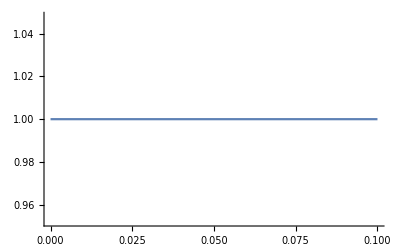

```mathematica
Plot[GammaRegularized[1/2,2 σρ^2] + Erf[√2 σρ], {σρ, 0, 0.1}]
```

```mathematica
ωx=Sin[θ]Cos[ϕ];
ωy=Sin[θ]Sin[ϕ];
ωz=Cos[θ];
one=GammaRegularized[1/2,σρ^2/2] + Erf[σρ/(√2)];
oone=GammaRegularized[1/2,2 σρ^2] + Erf[√2 σρ];
```

```mathematica
Simplify[cxx-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) ((ⅇ^(2 σθ^2)-1)( 1-ωx^2)(3-oone)/2+(1+ ⅇ^(2 σθ^2)) ωx^2(3-oone )-4  ⅇ^(σθ^2-σρ^2) ωx^2(2-one)))]
```

0

```mathematica
Simplify[cyy-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) ( (ⅇ^(2 σθ^2)-1)( 1-ωy^2)(3-oone)/2+(1+ ⅇ^(2 σθ^2)) ωy^2(3-oone )-4 ⅇ^(σθ^2-σρ^2) ωy^2(2-one) ))]
```

0

```mathematica
Simplify[czz-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) ( (ⅇ^(2 σθ^2)-1)+ωz^2(3+ⅇ^(2 σθ^2)-4 ⅇ^(σθ^2-σρ^2) )))]
```

0

```mathematica
Simplify[cxy-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) (3+ⅇ^(2 σθ^2)-4 ⅇ^(σθ^2-σρ^2)) ωx ωy)]
Simplify[cxz-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) (3+ⅇ^(2 σθ^2)-4 ⅇ^(σθ^2-σρ^2)) ωx ωz)]
Simplify[cyz-(1/4 ⅇ^(-2 σθ^2+2 σρ^2) (3+ⅇ^(2 σθ^2)-4 ⅇ^(σθ^2-σρ^2)) ωz ωy)]
```

0

0

0

```mathematica
M=1/2 ⅇ^(-σθ^2+2 σρ^2)((ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) {{0,  ωx ωy, ωx ωz },{ωx ωy, 0, ωy ωz},{ωx ωz,ωy ωz ,ωz^2}}+Sinh[σθ^2]{{0,  0,0 },{0, 0,0},{0,0 , 1}});
M//MatrixForm
Simplify[{{0, cxy, cxz}, {cxy, 0, cyz}, {cxz, cyz, czz}}-M]//MatrixForm
```

(0 | 1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[ϕ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ]^2 Sin[ϕ] | 1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[θ] Cos[ϕ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ]
1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[ϕ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ]^2 Sin[ϕ] | 0 | 1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[θ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ] Sin[ϕ]
1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[θ] Cos[ϕ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ] | 1/2 ⅇ^(-σθ^2+2 σρ^2) Cos[θ] (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2]) Sin[θ] Sin[ϕ] | 1/2 ⅇ^(-σθ^2+2 σρ^2) (Cos[θ]^2 (ⅇ^(-σθ^2)-2 ⅇ^(-σρ^2)+Cosh[σθ^2])+Sinh[σθ^2]))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)